## The Literate Turtle

```mathematica
Nest[StringReplace[#,"F"->"F+F--F+F"]&,"F",3]
```

F+F--F+F+F+F--F+F--F+F--F+F+F+F--F+F+F+F--F+F+F+F--F+F--F+F--F+F+F+F--F+F--F+F--F+F+F+F--F+F--F+F--F+F+F+F--F+F+F+F--F+F+F+F--F+F--F+F--F+F+F+F--F+F

```mathematica
Options[FractalTurtleBasic]={PlotStyle->Thickness[0.01]};
FractalTurtleBasic[rewrite_,start_String,d_Integer,angle_,opts___]:=Module[
{dir={1,0},rotleft,rotright, sty, lastpt, chars, ang=N[angle Degree]},
sty=PlotStyle/.{opts}/.Options[FractalTurtleBasic];
If[!ListQ[sty], sty = {sty}];
{rotleft, rotright}=RotationTransform /@ ({-1,1} ang);
chars= Characters[Nest[StringReplace[#,rewrite]&,start,d]];
pts=Reap[Sow[lastpt={0,0}]⟦1⟧;
Do[Which[
c=="+",dir=rotleft[dir],
c=="-",dir=rotright[dir],
c=="F",Sow[lastpt+=dir],
c=="B",Sow[lastpt-=dir],
c=="i",{rotleft,rotright}={rotright,rotleft}],{c,chars}]]⟦2⟧;
Graphics[Append[sty, Line[pts]],Sequence@@FilterRules[{opts},Options[Graphics]],PlotRange->All]]
```

```mathematica
FractalTurtleBasic[r_,s_String,depths_List,angle_, opts___]:=GraphicsGrid[Map[FractalTurtleBasic[r,s,#,angle, opts]&,depths,{Depth[depths]-1}]]
```

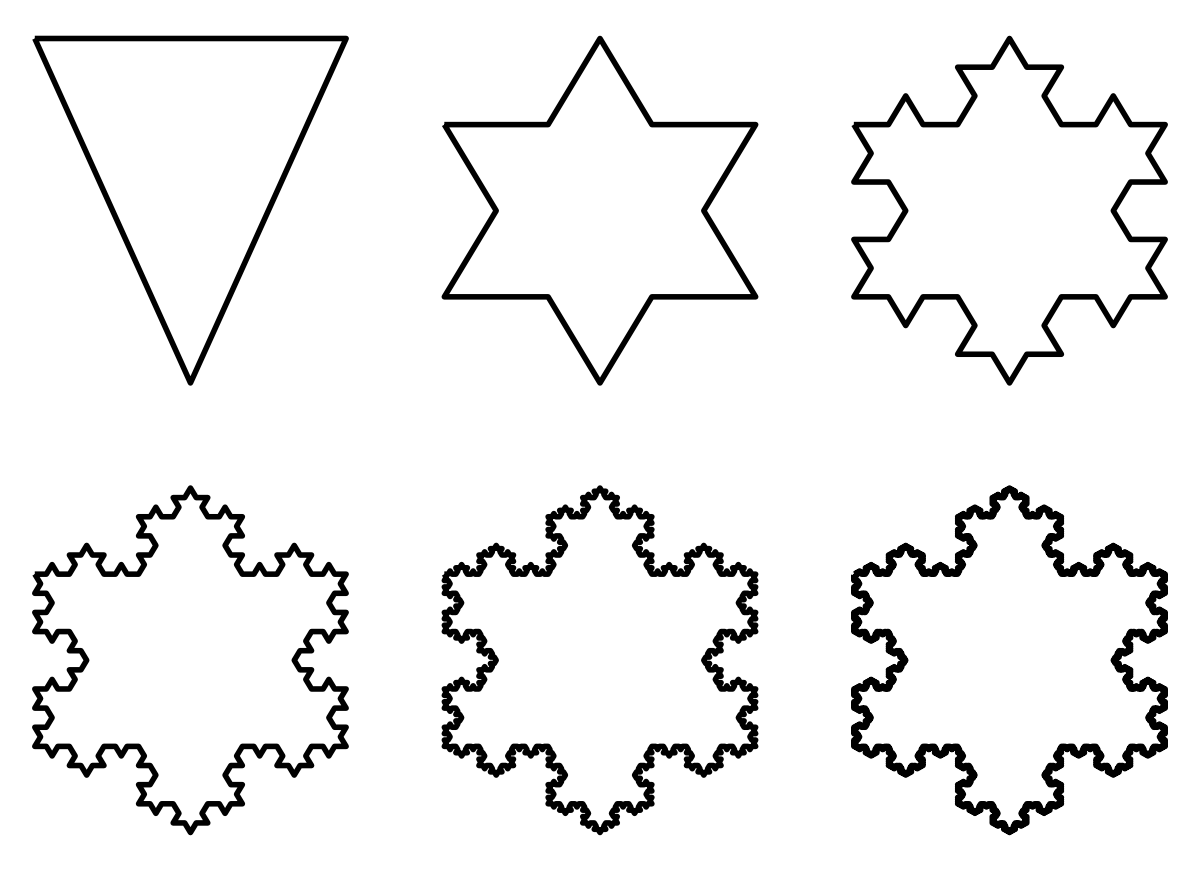

```mathematica
FractalTurtleBasic["F"->"F-F++F-F","F++F++F",{{0,1,2},{3,4,5}},60]
```

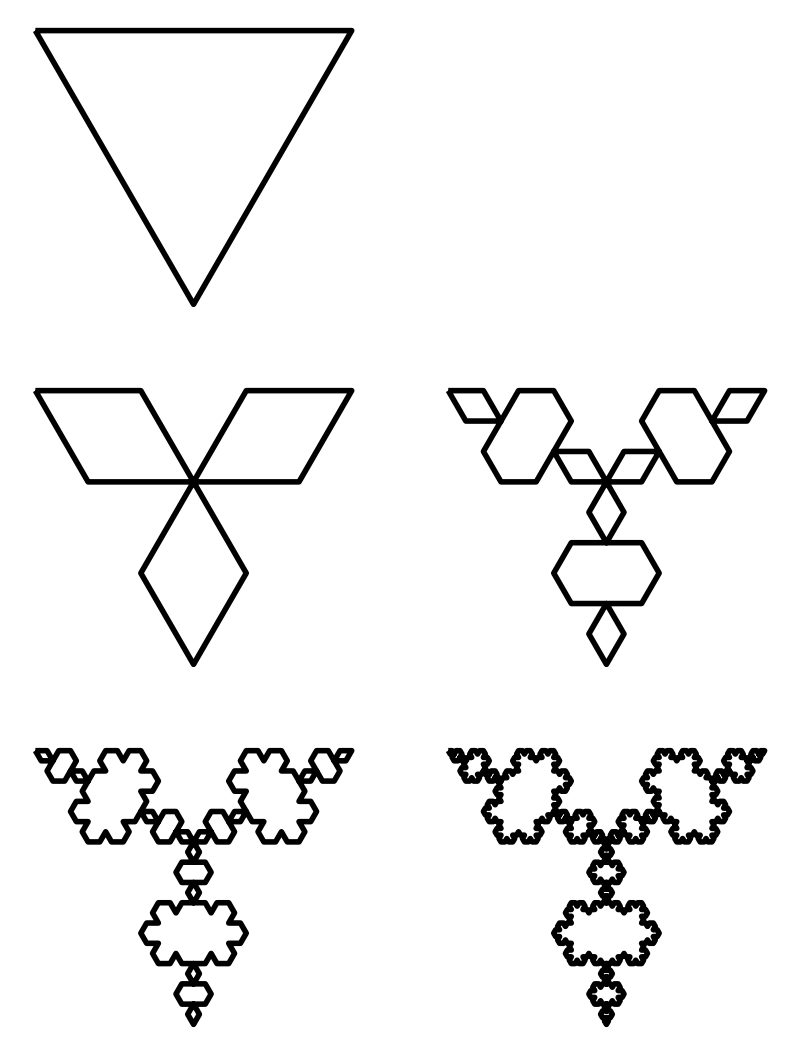

```mathematica
FractalTurtleBasic["F"->"F+F--F+F","F++F++F",{{0},{1,2},{3,4}},60]
```

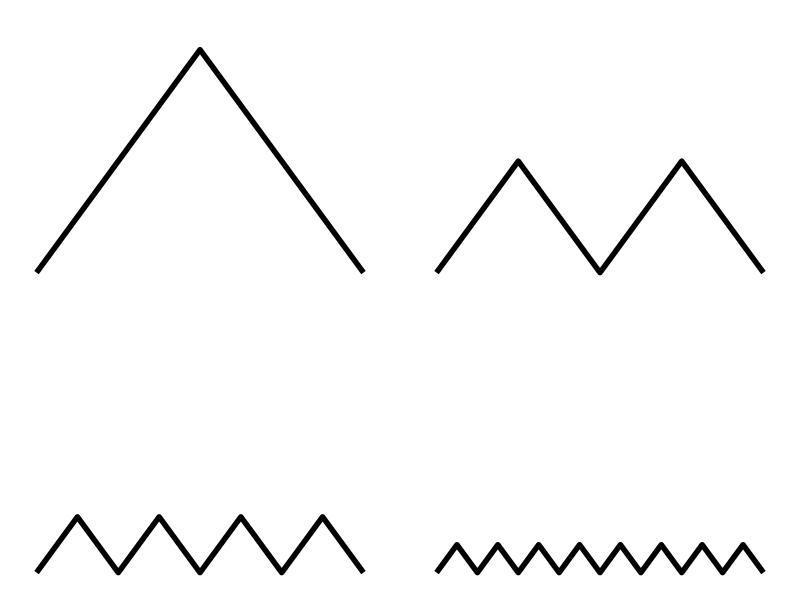

```mathematica
Grid[Partition[
Table[FractalTurtle["X"->"XX","X",i,90,
		StartDirection->{1,1},TurtleStep->2^(-(i+1)),TerminalSubstitution->"X"->"F-F+",Frame->False,Axes->Automatic,PlotRange->{0,0.55}],{i,0,3}],2]]
```